## MATEMÁTICAS

### Cálculo y álgebra lineal

D[f,x[ es la derivada, Integrate[f,{x,a,b}] el área acumulada con signo.

Series expande en potencias.

LinearSolve[A,b] resuelve para una matriz A x=b.

Los auto-valores λ cumplen A*v=λ*v. El producto matricial es A.b

#### Derivación e Integración

```mathematica
D[x*x*x*Sin[x],x]
```

x^3 Cos[x]+3 x^2 Sin[x]

```mathematica
Integrate[x*x,{x,0,3}]
```

9

```mathematica
Integrate[x*x,x]
```

x^3/3

```mathematica
Series[Exp[x],{x,0,4}]
```

1+x+x^2/2+x^3/6+x^4/24+O[x]^5

#### Álgebra lineal

definimos la matriz

```mathematica
A={{2,1},{1,3}}
```

{{2,1},{1,3}}

solo con listas {} confirmando lo basico de mathematica funciones usan principalmente para sus argumentos []

```mathematica
LinearSolve[A,{1,2}]
```

{1/5,3/5}

```mathematica
A.{1/5,2/5}
```

{4/5,7/5}

```mathematica
MatrixForm[A]
```

(2 | 1
1 | 3)

```mathematica
N[Eigenvalues[A]]
```

{3.61803,1.38197}

```mathematica
Eigenvectors[A]
```

{{1/2 (-1+√5),1},{1/2 (-1-√5),1}}

#### EDOS y optimización

```mathematica
ClearAll["Global'*"]
```

```mathematica
sol=DSolve[{T'[t]==-k(T[t]-Ta), T[0]==T0},T[t],t]
```

{{T[t]→20. ⅇ^(-0.1 t) (3.+1. ⅇ^(0.1 t))}}

Este comando DSolve[ {expresion , con condicion inicialales },expresion funcion con respecto a que, lo mismo si hay derivadas, variable independiente]

NO SIRVEPARA PLOTEAR

```mathematica
?DSolve
```

```mathematica
ysol = NDSolveValue[{y'[t] == -0.3 y[t] + 2, y[0] == 0}, y, {t, 0, 20}]
ysol[20]
```

NDSOLVEVALUE[{ECUACION DIFERENCIAL, { CONDICIONES INCIALES SI ES UNA SIN {}}}, RESPECTO QUE FUNCION SIN [] SINO EN SECO PURA F O Y , {VARIABLE INDE PENDIENTES, INICIAL, FINAL}                  ]

InterpolatingFunction[…]

6.65014

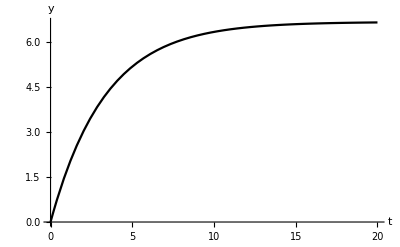

```mathematica
Plot[ysol[t], {t, 0, 20}, AxesLabel -> {"t", "y"}]
```

```mathematica
k=0.1;
Ta=20;
T0=80;
```

```mathematica
Plot[sol, {t, -3, 3}, PlotLabel -> "Solución de y'[t] == t^2"] (*VES NO SIRVE*)
```

-Graphics-

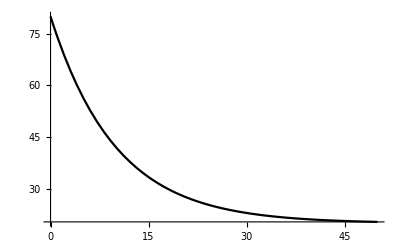

```mathematica
k=0.1;
Ta=20;
T0=80;

Plot[M,{t,0,50}]
```

```mathematica
M=DSolveValue[{T'[t]==-k*(T[t]-Ta),T[0]==T0},T[t],{t,0,50}]
```

20.+60. ⅇ^(-0.1 t)

```mathematica
Minimize[x^2 - 4 x + 3, x]
f[x_] := x^4 - 3 x^2 + x
FindMinimum[f[x], {x, 1}] (* empieza a buscar desde {x=1) *)
NMinimize[f[x], x](*NMinize es el bueno *)
```

{-1,{x→2}}

{-1.07023,{x→1.1309}}

{-3.51391,{x→-1.30084}}

```mathematica
FindMinimum[f[x],x]
```

{-1.07023,{x→1.1309}}

#### Ajuste de datos y estadística

```mathematica
ClearAll["Global`*"]
datos = {{1, 2.1}, {2, 3.9}, {3, 6.2}, {4, 7.8}, {5, 10.1}} (* datos van en lista (forman matriz) *)
MatrixForm[datos]
lm = LinearModelFit[datos, x, x](* ajusta a una funcion que depende de la variable x, [datos, funcion que quiero que se ajuste, variable de la función ]*)
Normal[lm]
lm["BestFitParameters"]
lm["RSquared"]
lm["FitResiduals"]
```

```mathematica
{{1,2.1},{2,3.9},{3,6.2},{4,7.8},{5,10.1}}
```

(1 | 2.1
2 | 3.9
3 | 6.2
4 | 7.8
5 | 10.1)

FittedModel[0.05+1.99 x]

0.05+1.99 x

{0.05,1.99}

0.997305

{0.06,-0.13,0.18,-0.21,0.1}

```mathematica
lista1={0.060000000000001386,-0.12999999999999945,0.17999999999999972,-0.21000000000000174,0.09999999999999787}
```

{0.06,-0.13,0.18,-0.21,0.1}

```mathematica
Thread[{Range[Length[lista1]], lista1}]
```

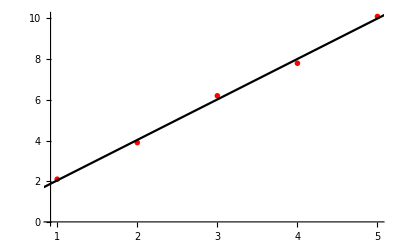

```mathematica
Show[ListPlot[datos, PlotStyle -> {Red, PointSize[0.03]}],
Plot[lm[x], {x, 0, 6}]]
```

```mathematica
Interpolation[datos][2.5]
```

5.0625

```mathematica
SeedRandom[1]
```

esta función fija números al “azar” o sea aleatorios seleccionados y con esos siempre trabajará o sea a partir de aquí los números aleatorios quedan “clavados” pertenecen a seedrandom 1

```mathematica
?NormalDistribution
```

```mathematica
?RandomVariate
```

```mathematica
m=RandomVariate[NormalDistribution[50,10],200]
```

{45.4244,62.7215,55.2428,55.3772,48.1635,49.773,58.1363,47.5541,50.6142,38.6714,55.7639,41.6486,49.4475,42.1666,55.0423,53.5814,38.6361,58.402,54.2962,65.5067,44.6081,49.4646,43.893,52.5242,42.1055,46.8625,43.2425,61.7145,53.8667,49.5076,50.7583,67.8078,42.3866,58.3476,48.0168,50.6347,56.7964,53.1986,49.1488,37.3228,37.2676,54.1001,38.1864,48.1295,74.0468,43.4124,35.8945,52.4835,52.0695,45.1531,34.9953,52.094,28.3587,42.6035,40.5325,40.7535,44.6219,54.1326,53.2519,52.7354,42.3988,37.4084,49.3148,45.7535,56.9744,32.3265,43.005,53.4864,54.642,48.9313,57.2144,55.2482,53.4052,56.7253,37.3244,57.0237,43.7005,48.1042,67.9968,50.9109,52.8723,46.0957,53.7955,44.7149,34.378,46.3549,37.3583,40.4172,38.7271,47.9822,43.9181,51.5356,42.324,45.6247,52.1881,38.5877,32.4574,45.8765,47.9117,59.0177,53.4099,54.1283,49.6121,38.666,45.1787,73.513,37.5755,49.5856,63.8467,49.5009,50.3098,53.8946,64.3382,40.1492,49.9683,40.0427,94.4453,50.691,67.0277,47.3949,46.3204,59.8705,23.4984,59.8317,51.3073,31.9718,33.9764,37.3385,49.1278,54.3338,51.168,53.151,57.4657,46.0467,41.9333,62.8429,59.0414,44.8919,43.7632,56.528,45.5623,50.5805,48.6919,50.6693,57.7147,40.539,54.6063,45.5611,58.7124,33.8277,56.2795,34.5977,39.2363,41.5701,59.2152,64.0848,40.2757,60.7828,55.0449,59.2263,47.4285,61.6847,38.382,65.5762,45.6234,35.6698,53.136,71.6539,43.1231,55.5769,47.3751,43.3915,47.4334,56.1229,59.1673,54.3378,77.3326,68.824,48.9928,76.1792,28.3232,58.1554,49.6558,25.8135,44.4869,52.1105,33.9363,38.2824,54.5057,57.5984,47.1079,63.312,68.0576,37.032,46.9081,51.6832,44.7632,49.3303,61.5008,58.9854}

```mathematica
NormalDistribution[100,5]
```

NormalDistribution[100,5]

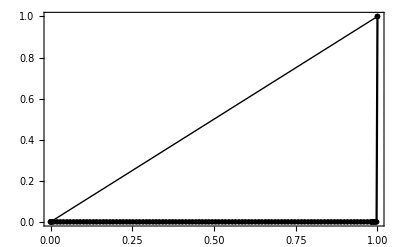

```mathematica
ProbabilityPlot[NormalDistribution[50,2]]
```

```mathematica
{Mean[m], StandardDeviation[m]}
```

{49.7513,10.1367}

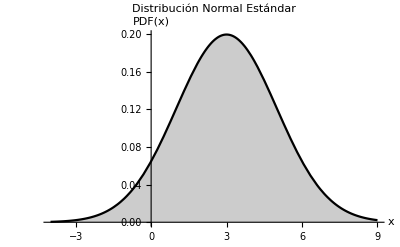

```mathematica
Plot[PDF[NormalDistribution[3,2],x],{x,-4,9},PlotLabel->"Distribución Normal Estándar",AxesLabel->{"x","PDF(x)"},Filling->Axis]
```

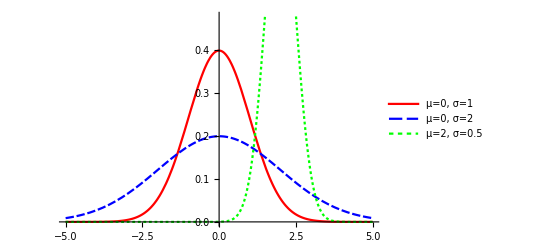

```mathematica
Plot[{PDF[NormalDistribution[0,1],x],PDF[NormalDistribution[0,2],x],PDF[NormalDistribution[2,0.5],x]},{x,-5,5},PlotLegends->{"μ=0, σ=1","μ=0, σ=2","μ=2, σ=0.5"},PlotStyle->{Red,Blue,Green}]
```